# Woods-Saxon Potential

## Micah Buuck

6/12/13

## Constants and Initial Conditions

Originally I tried to make use of Mathematica's built-in unit handling, but I couldn't figure out how to make that work with plotting, so I gave up. I left the code for it in, but commented it out.

```mathematica
(*<<Units`
Needs["PhysicalConstants`"]*)
```

```mathematica
R=3 (*Femto Meter*);
V0=-50 (*Mega ElectronVolt*);
a=.54 (*Femto Meter*);
V[r_]:=V0/(1+E^((r-R)/a));
m=938.272046(*Mega ElectronVolt*);
ℏc=197.32697178(*Mega ElectronVolt^2*Femto Meter^2*);
```

### Plot for potential

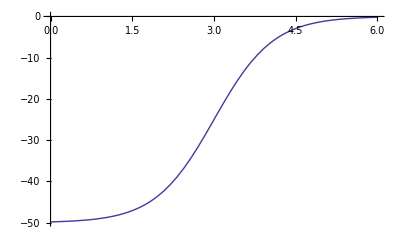

```mathematica
Plot[V[r],{r,0,2*R}]
```

## Solve the Schrödinger Equation

First I solve the Schrödinger equation for the radial wavefunction with an arbitrary constant for the initial condition for u'(0). My goal is to show that the resulting phase shift we get from this in independent of the choice of u'(0).

```mathematica
s[L_,k_,b_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==b},u,{r,(1000*k)^(-1),5*R}]
```

```mathematica
u[L_,k_,r_,b_]:=u[r]/.s[L,k,b][[1]]
```

```mathematica
β[L_,k_,b_]:=5*R/Evaluate[u[L,k,5*R,b]]*(D[u[L,k,r,b],r]/.r->(5*R))-1
tanδ[L_,k_,b_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k,b]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k,b]*SphericalBesselY[L,k*5*R])]
```

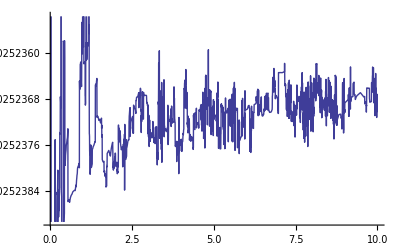

```mathematica
Plot[tanδ[0,1,b],{b,0.01,10}]
```

As we can see from this plot of tanδ vs. u'(0), the phase shift appears to be independent of our choice of u'(0) up to about 0.01% error.

## Reformulate tanδ for specific choice of u'(0)

These are the same equations as above, but now we have chosen u'(0)=8 (an arbitrary choice).

```mathematica
s[L_,k_]:=NDSolve[{u''[r]+(k^2-2*m/(ℏc)^2*V[r]-L*(L+1)/r^2)*u[r]==0,u[(1000*k)^(-1)]==0,u'[(1000*k)^(-1)]==8},u,{r,(1000*k)^(-1),5*R},MaxSteps->20000]
```

```mathematica
u[L_,k_,r_]:=u[r]/.s[L,k][[1]]
```

```mathematica
β[L_,k_]:=5*R/Evaluate[u[L,k,5*R]]*(D[u[L,k,r],r]/.r->(5*R))-1
tanδ[L_,k_]:=N[(k*5*R*Derivative[0,1][SphericalBesselJ][L,k*5*R]-β[L,k]*SphericalBesselJ[L,k*5*R])/(k*5*R*Derivative[0,1][SphericalBesselY][L,k*5*R]-β[L,k]*SphericalBesselY[L,k*5*R])]
```

```mathematica
Table[tanδ[L,1],{L,0,20}]
```

{-0.498341,-0.740053,-1.40718,-9.04647,0.345919,0.0544545,0.0105089,0.00210731,0.000424391,0.0000852015,0.0000170165,3.39049×10^-6,6.73638×10^-7,1.33352×10^-7,3.30182×10^-8,7.27915×10^-9,1.19763×10^-9,1.49402×10^-10,3.04508×10^-12,-2.23543×10^-12,-3.39837×10^-13}

```mathematica
u[0,1,1]
```

4.19436

For k=1, tanδ becomes negligible after about L=5. This is also evident in the plot for continuous L below.

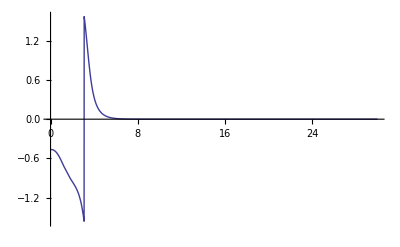

```mathematica
Plot[ArcTan[tanδ[L,1]],{L,0,30},PlotRange->{-Pi/2,Pi/2}]
```

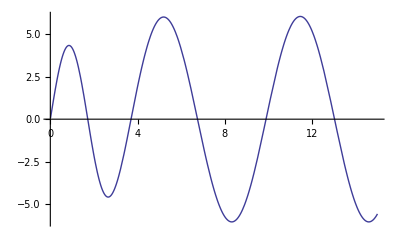

```mathematica
Plot[Evaluate[u[0,1,r]],{r,(100)^(-1),5*R}]
```

Plugging this phase shift into the equations for the scattering amplitude is:

```mathematica
Clear[f]
```

```mathematica
f[k_,θ_]:=1/k*Sum[(2*L+1)*tanδ[L,k]/(1-I*tanδ[L,k])*LegendreP[L,Cos[θ]],{L,0,2*k*R}]
```

Here is a table of some values of dσ/dΩ as a function of θ.

```mathematica
tab=Table[{θ,Abs[f[1,θ]]^2},{θ,0,Pi,.1}]
```

{{0.,158.075},{0.1,150.799},{0.2,130.835},{0.3,103.031},{0.4,73.4285},{0.5,47.2829},{0.6,27.7653},{0.7,15.6797},{0.8,9.99381},{0.9,8.70802},{1.,9.64866},{1.1,10.9937},{1.2,11.535},{1.3,10.7542},{1.4,8.76954},{1.5,6.17032},{1.6,3.75227},{1.7,2.2051},{1.8,1.8447},{1.9,2.49214},{2.,3.55793},{2.1,4.3077},{2.2,4.20314},{2.3,3.17055},{2.4,1.67211},{2.5,0.535875},{2.6,0.60559},{2.7,2.35409},{2.8,5.62719},{2.9,9.6356},{3.,13.2108},{3.1,15.229}}

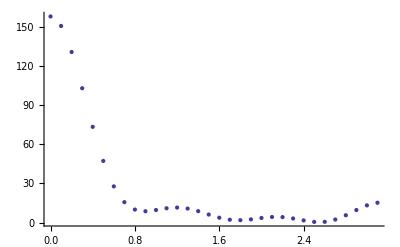

```mathematica
p=ListPlot[tab]
```

Here's a plot of that same information. This takes quite a while to evaluate.

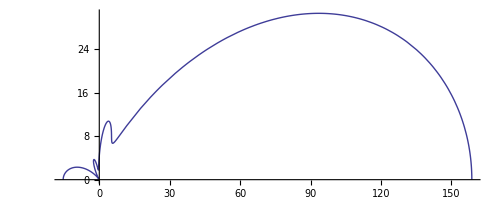

```mathematica
Plot[Abs[f[1,θ]]^2,{θ,0,Pi}]
```

## Eikonal Approximation

These equations come straight out of Sakurai, equations 7.4.13 and 7.4.14 (page 394).

```mathematica
Clear[Δ,Eif]
```

```mathematica
Δ[k_,b_?NumericQ]:=-m/(k*(ℏc)^2)*NIntegrate[V[Sqrt[b^2+z^2]],{z,0,Infinity}]
Eif[k_,θ_]:=-I*k*NIntegrate[b*BesselJ[0,k*b*θ]*(E^(2*I*Δ[1,b])-1),{b,0,Infinity}]
```

```mathematica
Δ[100,0]
```

0.03617

```mathematica
tab1=Table[{θ,Abs[Eif[1,θ]]^2},{θ,.1,Pi,.1}]
```

{{0.1,66.4948},{0.2,56.409},{0.3,42.5711},{0.4,28.2395},{0.5,16.1811},{0.6,7.92113},{0.7,3.59484},{0.8,2.3171},{0.9,2.78668},{1.,3.8249},{1.1,4.67298},{1.2,5.03092},{1.3,4.92791},{1.4,4.5427},{1.5,4.06032},{1.6,3.59974},{1.7,3.20423},{1.8,2.86638},{1.9,2.56048},{2.,2.26549},{2.1,1.97399},{2.2,1.69049},{2.3,1.425},{2.4,1.18682},{2.5,0.981035},{2.6,0.807978},{2.7,0.664525},{2.8,0.545984},{2.9,0.447655},{3.,0.365671},{3.1,0.297184}}

```mathematica
tab1={{0.,70.19400809127545},{0.1,66.49484753296754},{0.2,56.409006456132865},{0.30000000000000004,42.571092599603816},{0.4,28.239538523701963},{0.5,16.181078161413},{0.6,7.921126506958294},{0.7000000000000001,3.59484359809875},{0.8,2.3170991582326463},{0.9,2.786677920379093},{1.,3.8248987715660316},{1.1,4.672984888174993},{1.2000000000000002,5.030916670538743},{1.3000000000000003,4.9279130286517905},{1.4000000000000001,4.542701799639594},{1.5000000000000002,4.060317632854412},{1.6,3.599744267137363},{1.7000000000000002,3.204231959542861},{1.8000000000000003,2.8663809031328285},{1.9000000000000001,2.5604833209421134},{2.,2.2654889543318206},{2.1,1.973986900733205},{2.2,1.69049129161432},{2.3000000000000003,1.425004721162447},{2.4000000000000004,1.1868204839641279},{2.5000000000000004,0.9810346025308787},{2.6,0.8079780521423476},{2.7,0.6645247644651653},{2.8000000000000003,0.5459839774026526},{2.9000000000000004,0.44765518576632946},{3.0000000000000004,0.36567108793708647},{3.1,0.29718424888551986}}
```

{{0.,70.194},{0.1,66.4948},{0.2,56.409},{0.3,42.5711},{0.4,28.2395},{0.5,16.1811},{0.6,7.92113},{0.7,3.59484},{0.8,2.3171},{0.9,2.78668},{1.,3.8249},{1.1,4.67298},{1.2,5.03092},{1.3,4.92791},{1.4,4.5427},{1.5,4.06032},{1.6,3.59974},{1.7,3.20423},{1.8,2.86638},{1.9,2.56048},{2.,2.26549},{2.1,1.97399},{2.2,1.69049},{2.3,1.425},{2.4,1.18682},{2.5,0.981035},{2.6,0.807978},{2.7,0.664525},{2.8,0.545984},{2.9,0.447655},{3.,0.365671},{3.1,0.297184}}

The plot of the table above looks very different from the plot for the partial wave approximation. The most obvious difference is that there are no minima in the scattering amplitude like there are for the partial wave expansion. I'm not totally confident that the partial wave expansion is giving me the correct behavior, but a good way to check would be to look at the high k limit where these two should be in better agreement.

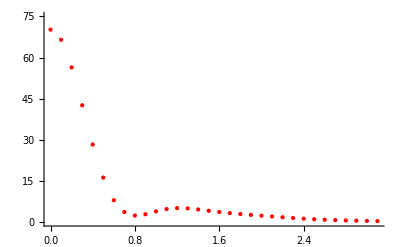

```mathematica
p1=ListPlot[tab1,PlotStyle->Red,PlotRange->{0,75}]
```

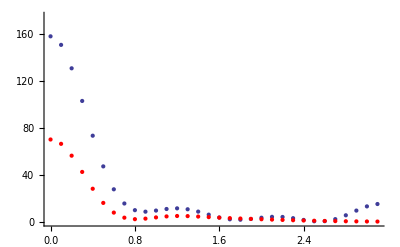

```mathematica
Show[p,p1,PlotRange->{0,175}]
```

I was not able to get a plot for the same information because it was taking too long to evaluate. I only let it run for about 10 minutes, so I think it would probably evaluate given enough time.

```mathematica
Plot[Abs[Eif[1,θ]]^2,{θ,0,Pi}]
```

## Born Approximation

Here we attempt the Born approximation and compare it to the two methods used above.

```mathematica
Bf[k_,θ_]:=-m/(ℏc^2*k*Sin[θ/2])*NIntegrate[r*V[r]*Sin[2*k*Sin[θ/2]*r],{r,0,Infinity}]
```

NIntegrate::deorela: The relative error 9.94291 is larger than expected for the integrand -50 r Sin[0.00006417824991232016` r]/1 + ⅇ^1.8518518518518516` (-3 + r) over {0, ∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10, 5}. The integration will proceed with TuningParameters -> {1, 5}.

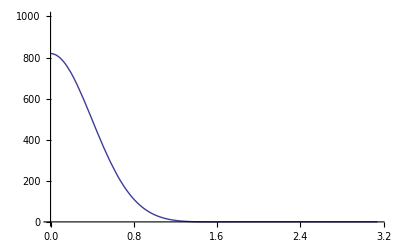

```mathematica
Plot[Abs[Bf[1,θ]]^2,{θ,0,Pi},PlotRange->{{0,Pi},{0,1000}}]
```

```mathematica
.5*V[.5]*Sin[2*1*Sin[0/2]*.5]
```

0

## Check Method for k=10

For k=10, then k^2 = 100 >> 2*m*V/ℏ^2 ~= 2.5, so the eikonal approximation should be valid.

```mathematica
tab10pwe=Table[{θ,Abs[f[1,θ]]^2},{θ,0,Pi,.1}]
```

{{0.,158.189},{0.1,150.907},{0.2,130.909},{0.3,103.039},{0.4,73.3582},{0.5,47.173},{0.6,27.6835},{0.7,15.6698},{0.8,10.0428},{0.9,8.76624},{1.,9.67827},{1.1,10.9965},{1.2,11.5373},{1.3,10.7725},{1.4,8.79439},{1.5,6.18042},{1.6,3.73925},{1.7,2.18106},{1.8,1.82782},{1.9,2.48827},{2.,3.55758},{2.1,4.29942},{2.2,4.18732},{2.3,3.15877},{2.4,1.67359},{2.5,0.546581},{2.6,0.612451},{2.7,2.35085},{2.8,5.62532},{2.9,9.6576},{3.,13.2702},{3.1,15.3154}}

```mathematica
tab10pwe[[All,2]]=Log[tab10pwe[[All,2]]]
```

{6.68021,3.19739,-1.36737,-5.53352,-8.43129,-13.702,-12.0279,-12.9798,-13.5176,-14.228,-15.0487,-16.1442,-17.9191,-18.7474,-16.9927,-16.1133,-15.5907,-15.2465,-15.0153,-14.8631,-14.772,-14.7336,-14.7424,-14.7993,-14.9087,-15.0786,-15.3369,-15.7186,-16.3417,-17.5858,-18.6366,-15.3832}

```mathematica
tab10pwelog=tab10pwe
tab10pwe={{0.,796.4878999201208},{0.1,24.46864963532322},{0.2,0.25477525332135276},{0.30000000000000004,0.003952072320128917},{0.4,0.0002179399952953134},{0.5,1.120151765884792*^-6},{0.6000000000000001,5.9753469991634275*^-6},{0.7000000000000001,2.3065257212900176*^-6},{0.8,1.3470720954178573*^-6},{0.9,6.620088701250219*^-7},{1.,2.913719501320335*^-7},{1.1,9.74212930258943*^-8},{1.2000000000000002,1.651411107577723*^-8},{1.3,7.213199423790259*^-9},{1.4000000000000001,4.1703026726147305*^-8},{1.5,1.0048296295363878*^-7},{1.6,1.6944539503734594*^-7},{1.7000000000000002,2.3907640582942507*^-7},{1.8,3.0124448491606246*^-7},{1.9000000000000001,3.507702383445945*^-7},{2.,3.8424623495450037*^-7},{2.1,3.9926336212895077*^-7},{2.2,3.957887855576977*^-7},{2.3000000000000003,3.739024319474509*^-7},{2.4000000000000004,3.3512943845140004*^-7},{2.5,2.8277100392753154*^-7},{2.6,2.1841749772183716*^-7},{2.7,1.4910341558780257*^-7},{2.8000000000000003,7.996159742780497*^-8},{2.9000000000000004,2.3046118159140694*^-8},{3.,8.058333289390952*^-9},{3.1,2.0853667576728768*^-7}}
```

{{0.,6.68021},{0.1,3.19739},{0.2,-1.36737},{0.3,-5.53352},{0.4,-8.43129},{0.5,-13.702},{0.6,-12.0279},{0.7,-12.9798},{0.8,-13.5176},{0.9,-14.228},{1.,-15.0487},{1.1,-16.1442},{1.2,-17.9191},{1.3,-18.7474},{1.4,-16.9927},{1.5,-16.1133},{1.6,-15.5907},{1.7,-15.2465},{1.8,-15.0153},{1.9,-14.8631},{2.,-14.772},{2.1,-14.7336},{2.2,-14.7424},{2.3,-14.7993},{2.4,-14.9087},{2.5,-15.0786},{2.6,-15.3369},{2.7,-15.7186},{2.8,-16.3417},{2.9,-17.5858},{3.,-18.6366},{3.1,-15.3832}}

{{0.,796.488},{0.1,24.4686},{0.2,0.254775},{0.3,0.00395207},{0.4,0.00021794},{0.5,1.12015×10^-6},{0.6,5.97535×10^-6},{0.7,2.30653×10^-6},{0.8,1.34707×10^-6},{0.9,6.62009×10^-7},{1.,2.91372×10^-7},{1.1,9.74213×10^-8},{1.2,1.65141×10^-8},{1.3,7.2132×10^-9},{1.4,4.1703×10^-8},{1.5,1.00483×10^-7},{1.6,1.69445×10^-7},{1.7,2.39076×10^-7},{1.8,3.01244×10^-7},{1.9,3.5077×10^-7},{2.,3.84246×10^-7},{2.1,3.99263×10^-7},{2.2,3.95789×10^-7},{2.3,3.73902×10^-7},{2.4,3.35129×10^-7},{2.5,2.82771×10^-7},{2.6,2.18417×10^-7},{2.7,1.49103×10^-7},{2.8,7.99616×10^-8},{2.9,2.30461×10^-8},{3.,8.05833×10^-9},{3.1,2.08537×10^-7}}

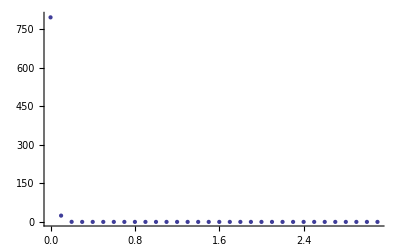

```mathematica
ListPlot[tab10pwe,PlotRange->{0,800}]
```

```mathematica
tab10eif=Table[{θ,Abs[Eif[10,θ]]^2},{θ,0.1,Pi,.1}]
```

{{0.1,382.49},{0.2,226.549},{0.3,36.5671},{0.4,3.90932},{0.5,0.341805},{0.6,0.026268},{0.7,0.00187147},{0.8,0.000121635},{0.9,8.01775×10^-6},{1.,4.33416×10^-7},{1.1,3.25687×10^-8},{1.2,1.26829×10^-9},{1.3,2.56199×10^-10},{1.4,8.17911×10^-11},{1.5,4.11128×10^-11},{1.6,2.64159×10^-11},{1.7,1.57317×10^-11},{1.8,9.97436×10^-12},{1.9,6.35722×10^-12},{2.,4.29168×10^-12},{2.1,3.0575×10^-12},{2.2,2.19536×10^-12},{2.3,1.53544×10^-12},{2.4,1.04701×10^-12},{2.5,7.25056×10^-13},{2.6,5.33259×10^-13},{2.7,4.01114×10^-13},{2.8,3.0171×10^-13},{2.9,2.27429×10^-13},{3.,1.72652×10^-13},{3.1,1.32398×10^-13}}

```mathematica
tab10eif={{0,7019.400809127545},{0.1,382.48987715660314},{0.2,226.5488954331821},{0.30000000000000004,36.56710879370866},{0.4,3.9093226854453027},{0.5,0.34180495024465574},{0.6,0.026267954235033773},{0.7000000000000001,0.0018714684991928965},{0.8,0.00012163519027454571},{0.9,8.017754173750536*^-6},{1.,4.334160532368528*^-7},{1.1,3.2568742879449145*^-8},{1.2000000000000002,1.2682892212203007*^-9},{1.3000000000000003,2.5619942527716535*^-10},{1.4000000000000001,8.179113522128039*^-11},{1.5000000000000002,4.1112756918641917*^-11},{1.6,2.6415936765107132*^-11},{1.7000000000000002,1.5731749668244962*^-11},{1.8000000000000003,9.974357633749364*^-12},{1.9000000000000001,6.357221156751615*^-12},{2.,4.291680896319437*^-12},{2.1,3.057496660640422*^-12},{2.2,2.195359988819458*^-12},{2.3000000000000003,1.535437445323493*^-12},{2.4000000000000004,1.0470115496454866*^-12},{2.5000000000000004,7.250558355592682*^-13},{2.6,5.332591123239962*^-13},{2.7,4.01113660651126*^-13},{2.8000000000000003,3.0170964640576976*^-13},{2.9000000000000004,2.274290779496665*^-13},{3.0000000000000004,1.7265209031635889*^-13},{3.1,1.323979328436138*^-13}}
```

{{0,7019.4},{0.1,382.49},{0.2,226.549},{0.3,36.5671},{0.4,3.90932},{0.5,0.341805},{0.6,0.026268},{0.7,0.00187147},{0.8,0.000121635},{0.9,8.01775×10^-6},{1.,4.33416×10^-7},{1.1,3.25687×10^-8},{1.2,1.26829×10^-9},{1.3,2.56199×10^-10},{1.4,8.17911×10^-11},{1.5,4.11128×10^-11},{1.6,2.64159×10^-11},{1.7,1.57317×10^-11},{1.8,9.97436×10^-12},{1.9,6.35722×10^-12},{2.,4.29168×10^-12},{2.1,3.0575×10^-12},{2.2,2.19536×10^-12},{2.3,1.53544×10^-12},{2.4,1.04701×10^-12},{2.5,7.25056×10^-13},{2.6,5.33259×10^-13},{2.7,4.01114×10^-13},{2.8,3.0171×10^-13},{2.9,2.27429×10^-13},{3.,1.72652×10^-13},{3.1,1.32398×10^-13}}

```mathematica
Im[Eif[10,0]]*4*Pi/10
```

95.0888

```mathematica
4*Pi/100*Sum[(2*L+1)*tanδ[L,10]^2/(1+tanδ[L,10]^2),{L,0,2*10*R}]
```

7.60163

```mathematica
7019.400809127545/796.4878999201208
```

8.81294

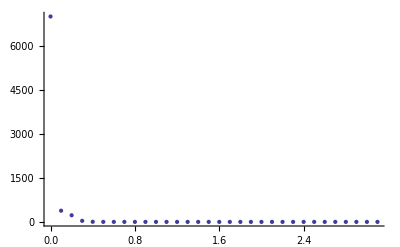

```mathematica
ListPlot[tab10eif,PlotRange->{0,7020}]
```